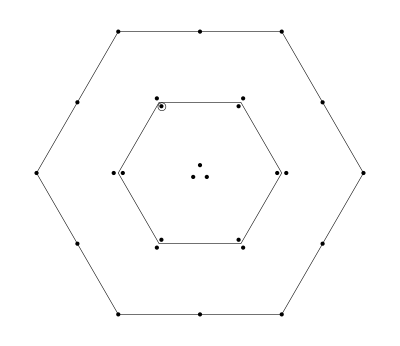

Y=1.5,  I_3=-0.5

-2(ud+du)(ūs̄+s̄ū)+dd(s̄d̄+d̄s̄)+(sd+ds)s̄s̄

```mathematica
(*-------------------------------*)
```

The current J:

(d_a^T C(γ̄)^5 d_b) ((d̄)_a(γ̄)^5 C((s̄)_b)^T+(d̄)_b(γ̄)^5 C((s̄)_a)^T)+((s̄)_a(γ̄)^5 C((s̄)_b)^T) (d_a^T C(γ̄)^5 s_b+s_a^T C(γ̄)^5 d_b)+(d_a^T C(γ̄)^5 d_b) ((s̄)_a(γ̄)^5 C((d̄)_b)^T+(s̄)_b(γ̄)^5 C((d̄)_a)^T)+((s̄)_b(γ̄)^5 C((s̄)_a)^T) (d_a^T C(γ̄)^5 s_b+s_a^T C(γ̄)^5 d_b)-2 (d_a^T C(γ̄)^5 u_b+u_a^T C(γ̄)^5 d_b) ((s̄)_a(γ̄)^5 C((ū)_b)^T)-2 (d_a^T C(γ̄)^5 u_b+u_a^T C(γ̄)^5 d_b) ((s̄)_b(γ̄)^5 C((ū)_a)^T)-2 (d_a^T C(γ̄)^5 u_b+u_a^T C(γ̄)^5 d_b) ((ū)_a(γ̄)^5 C((s̄)_b)^T)-2 (d_a^T C(γ̄)^5 u_b+u_a^T C(γ̄)^5 d_b) ((ū)_b(γ̄)^5 C((s̄)_a)^T)

the Fierz rearranged J (to naively get the decay partten)

```mathematica
-d̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 d-d̄ γ^μ d s̄ γ^μ d-s̄(γ^μ).(γ̄)^5 d s̄(γ^μ).(γ̄)^5 s-s̄ γ^μ d s̄ γ^μ s-s̄(γ̄)^5 d s̄(γ̄)^5 s+1/2 (d̄ σ^μν d s̄ σ^μν d)+1/2 (s̄ σ^μν d s̄ σ^μν s)+2 (s̄(γ^μ).(γ̄)^5 d ū(γ^μ).(γ̄)^5 u)+2 (s̄(γ^μ).(γ̄)^5 u ū(γ^μ).(γ̄)^5 d)+2 (s̄ γ^μ d ū γ^μ u)+2 (s̄ γ^μ u ū γ^μ d)+(s̄(γ̄)^5 d) (2 (ū(γ̄)^5 u)-d̄(γ̄)^5 d)+2 (s̄(γ̄)^5 u ū(γ̄)^5 d)-s̄ σ^μν d ū σ^μν u-s̄ σ^μν u ū σ^μν d+(s̄ 1d) (2 (ū 1u)-d̄ 1d)+2 (s̄ 1u ū 1d)-s̄ 1d s̄ 1s
```

Π(q^2)=
-(log(-q^2/μ^2) q^8)/(384 π^6)+(5 ⟨ GG ⟩ log(-q^2/μ^2) q^4)/(96 π^5)-(⟨ d̄ d⟩ log(-q^2/μ^2) (2 m_d-m_s-4 m_u) q^4)/(6 π^4)+(2 ⟨ ū u⟩ log(-q^2/μ^2) (m_d+m_s-m_u) q^4)/(3 π^4)+(⟨ s̄ s⟩ log(-q^2/μ^2) (m_d-2 m_s+4 m_u) q^4)/(6 π^4)-(4 ⟨ d̄ d⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(4 ⟨ s̄ s⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)-(8 ⟨ ū u⟩^2 log(-q^2/μ^2) q^2)/(3 π^2)+(25 ⟨G^3⟩ log(-q^2/μ^2) q^2)/(864 π^6)-(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(8 ⟨ d̄ d⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)-(8 ⟨ s̄ s⟩ ⟨ ū u⟩ log(-q^2/μ^2) q^2)/(3 π^2)+(59 ⟨ d̄ d⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(72 π^2)+(59 ⟨ s̄ s⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(72 π^2)+(49 ⟨ ū u⟩ ⟨ d̄ Gd⟩ log(-q^2/μ^2))/(36 π^2)+(59 ⟨ d̄ d⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(72 π^2)+(59 ⟨ s̄ s⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(72 π^2)+(49 ⟨ ū u⟩ ⟨ s̄ Gs⟩ log(-q^2/μ^2))/(36 π^2)+(49 ⟨ d̄ d⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(36 π^2)+(49 ⟨ s̄ s⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(36 π^2)+(23 ⟨ ū u⟩ ⟨ ū Gu⟩ log(-q^2/μ^2))/(18 π^2)-(⟨ GG ⟩ ⟨ d̄ d⟩^2)/(6 π q^2)-(⟨ GG ⟩ ⟨ s̄ s⟩^2)/(6 π q^2)-(8 ⟨ GG ⟩ ⟨ ū u⟩^2)/(9 π q^2)-(151 ⟨ d̄ Gd⟩^2)/(1152 π^2 q^2)-(151 ⟨ s̄ Gs⟩^2)/(1152 π^2 q^2)-⟨ ū Gu⟩^2/(24 π^2 q^2)-(⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ s̄ s⟩)/(3 π q^2)+(4 ⟨ GG ⟩ ⟨ d̄ d⟩ ⟨ ū u⟩)/(3 π q^2)+(4 ⟨ GG ⟩ ⟨ s̄ s⟩ ⟨ ū u⟩)/(3 π q^2)-(151 ⟨ d̄ Gd⟩ ⟨ s̄ Gs⟩)/(576 π^2 q^2)-(133 ⟨ d̄ Gd⟩ ⟨ ū Gu⟩)/(144 π^2 q^2)-(133 ⟨ s̄ Gs⟩ ⟨ ū Gu⟩)/(144 π^2 q^2)-(16 ⟨ d̄ d⟩^3 m_d)/(9 q^2)-(16 ⟨ d̄ d⟩ ⟨ s̄ s⟩^2 m_d)/(3 q^2)-(16 ⟨ s̄ s⟩^3 m_s)/(9 q^2)-(16 ⟨ d̄ d⟩^2 ⟨ s̄ s⟩ m_s)/(3 q^2)+(32 ⟨ s̄ s⟩^2 ⟨ ū u⟩ (2 m_d+m_s))/(9 q^2)+(32 ⟨ d̄ d⟩^2 ⟨ ū u⟩ (m_d+2 m_s))/(9 q^2)-(8 ⟨ d̄ d⟩ ⟨ ū u⟩^2 (4 m_d-8 m_s+8 m_u))/(9 q^2)-(8 ⟨ s̄ s⟩ ⟨ ū u⟩^2 (-8 m_d+4 m_s+8 m_u))/(9 q^2)+(8 ⟨ d̄ d⟩ ⟨ s̄ s⟩ ⟨ ū u⟩ (4 m_d+4 m_s+32 m_u))/(9 q^2)

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=η_8=η_10=1

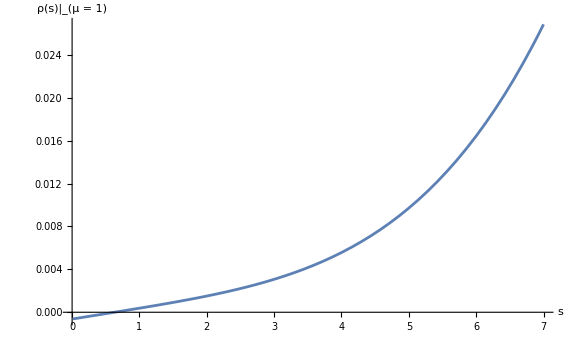
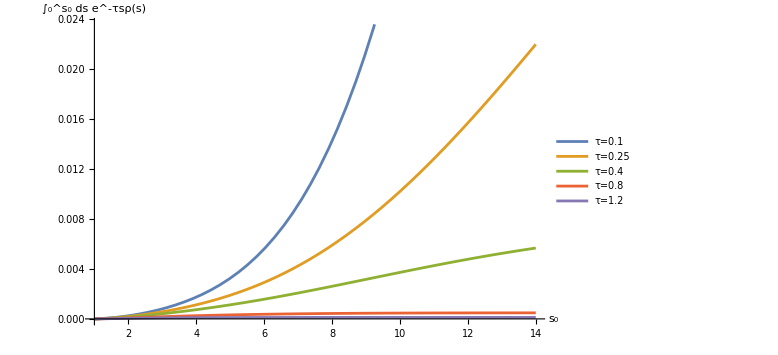

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=η_8=η_10=1

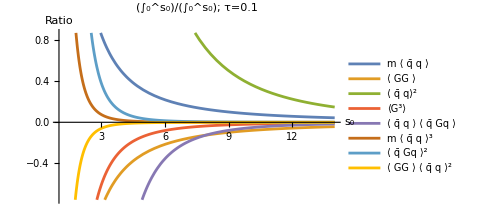
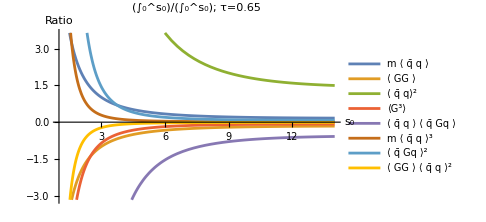
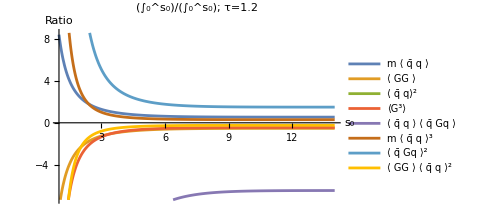

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=η_8=η_10=1

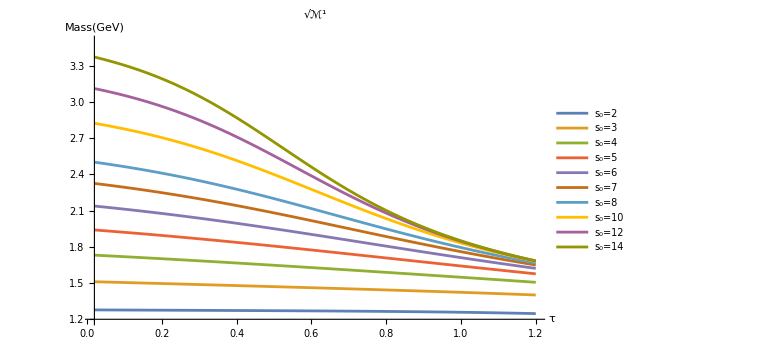
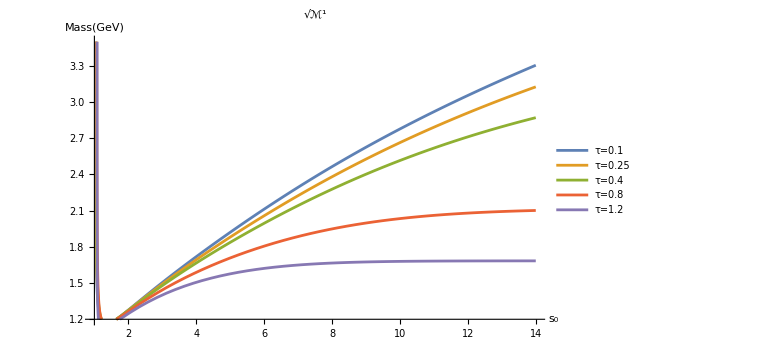

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=η_8=η_10=1

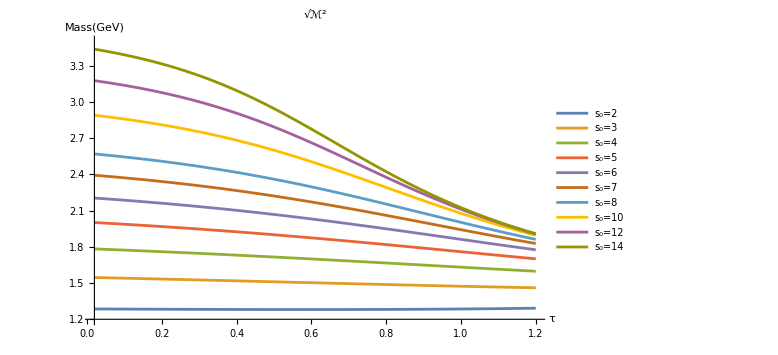
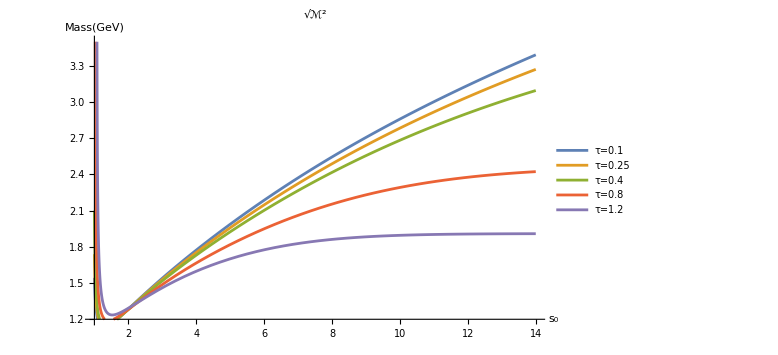

```mathematica
(*-------------------------------*)
```

ℳ^0(s_0) for η_6=3, η_8=5, η_10=5

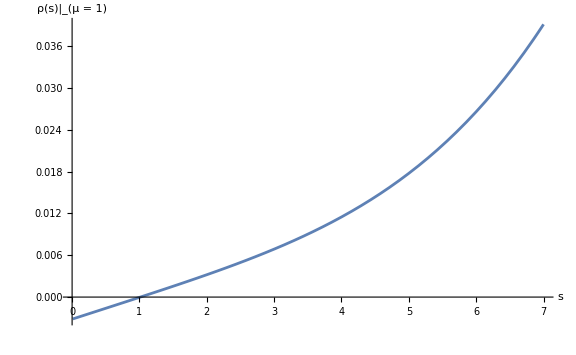
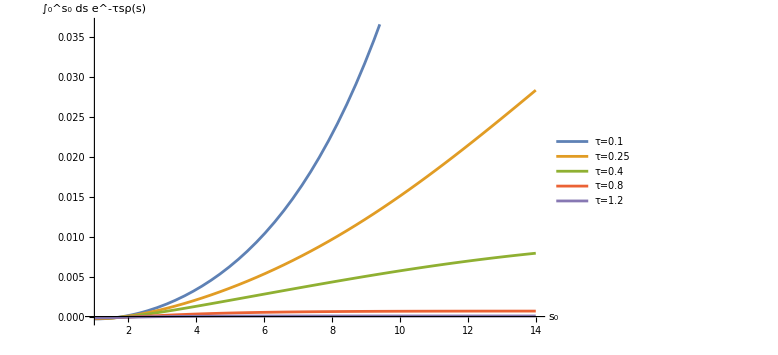

```mathematica
(*-------------------------------*)
```

(∫_0^s_0 dsC^i (s) ⟨𝒪_i⟩)/(∫_0^s_0 dsC^0 (s)) for η_6=3, η_8=5, η_10=5

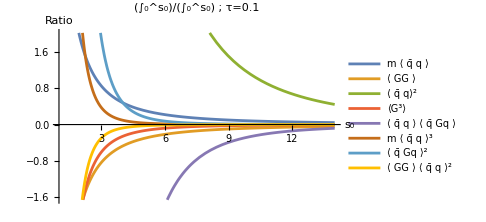
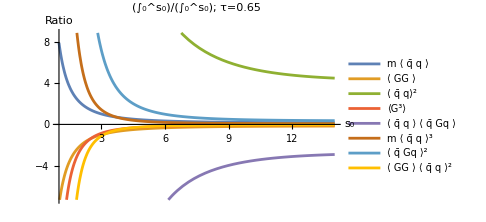
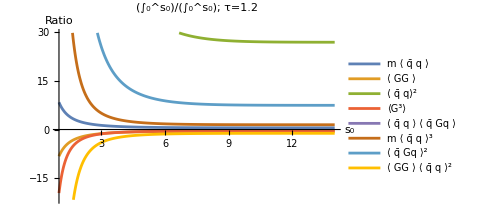

```mathematica
(*-------------------------------*)
```

ℛ^0 for η_6=3, η_8=5, η_10=5

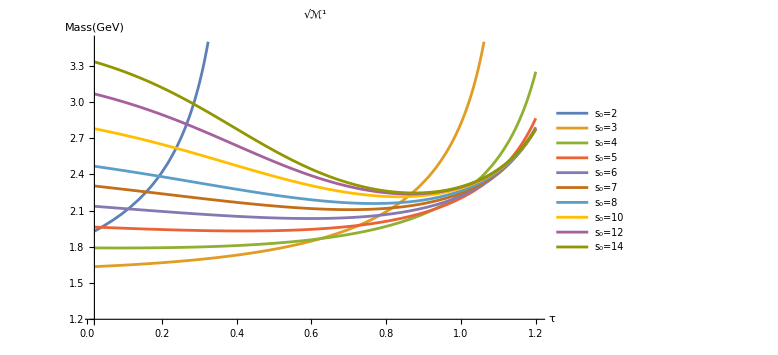
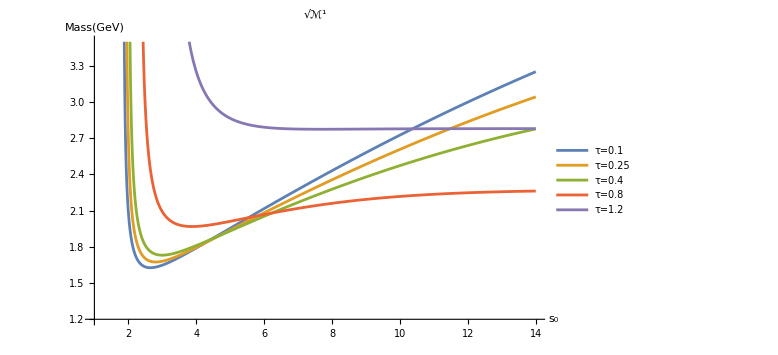

```mathematica
(*-------------------------------*)
```

ℛ^1 for η_6=3, η_8=5, η_10=5